```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/SLattice/peak_theory

```mathematica
npeak=2^4
```

16

```mathematica
mapdata=Import["data/mono_map_0.dat"][[1]];
```

```mathematica
NL=Length[mapdata]^(1/3)
```

256

```mathematica
dn=2^2;
map3D=Flatten[Table[{nx,ny,nz,mapdata[[NL^2(nx-1)+NL(ny-1)+nz]]},{nx,1,NL,dn},{ny,1,NL,dn},{nz,1,NL,dn}],2];
```

```mathematica
ListDensityPlot3D[map3D,PlotLegends->BarLegend[Automatic,LegendLabel->g[x,y,z]]]
```

-Graphics3D-

```mathematica
powerdata=Import["data/mono_power_0.dat"][[1]];
```

```mathematica
powerList=Table[{i-1,powerdata[[i]]},{i,Length[powerdata]}];
```

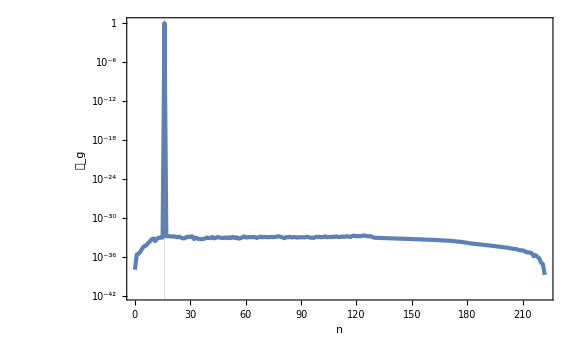

```mathematica
ListLogPlot[powerList,GridLines->{{npeak},None},FrameLabel->{n,Subscript[𝒫, g]}]
```

```mathematica
biasedmap=Import["data/mono_biased_0.dat"][[1]];
lapmap=Import["data/mono_laplacian_0.dat"][[1]];
```

```mathematica
shiftedmap2D=Flatten[Table[If[ny<0,nyt=ny+NL,nyt=ny];
If[nz<0,nzt=nz+NL,nzt=nz];
{ny,nz,biasedmap[[NL nyt+nzt+1]]},{ny,-NL/2+1,NL/2},{nz,-NL/2+1,NL/2}],1];
```

```mathematica
ListPlot3D[shiftedmap2D,PlotRange->Full,AxesLabel->{y,z,g},ColorFunction->ColorData["Gradients"][[37]],Mesh->None]
```

-Graphics3D-

```mathematica
focusedmap2D=Flatten[Table[If[ny<0,nyt=ny+NL,nyt=ny];
If[nz<0,nzt=nz+NL,nzt=nz];
{ny,nz,biasedmap[[NL nyt+nzt+1]]},{ny,-2npeak,2npeak},{nz,-2npeak,2npeak}],1];
```

```mathematica
ListPlot3D[focusedmap2D,PlotRange->Full,AxesLabel->{y,z,g},ColorFunction->ColorData["Gradients"][[37]],Mesh->None]
```

-Graphics3D-

```mathematica
lapmap2D=Flatten[Table[If[ny<0,nyt=ny+NL,nyt=ny];
If[nz<0,nzt=nz+NL,nzt=nz];
{ny,nz,lapmap[[NL nyt+nzt+1]]},{ny,-NL/2+1,NL/2},{nz,-NL/2+1,NL/2}],1];
```

```mathematica
ListPlot3D[lapmap2D,PlotRange->Full,AxesLabel->{y,z,"∇^2 g"},ColorFunction->ColorData["Gradients"][[37]],Mesh->None]
```

-Graphics3D-

```mathematica
focusedlap2D=Flatten[Table[If[ny<0,nyt=ny+NL,nyt=ny];
If[nz<0,nzt=nz+NL,nzt=nz];
{ny,nz,lapmap[[NL nyt+nzt+1]]},{ny,-2npeak,2npeak},{nz,-2npeak,2npeak}],1];
```

```mathematica
ListPlot3D[focusedlap2D,PlotRange->Full,AxesLabel->{y,z,"∇^2 g"},ColorFunction->ColorData["Gradients"][[37]],Mesh->None]
```

-Graphics3D-